# Connectome Explorer

## Find sub-circuit connecting two sets of neurons in a nervous system

## Step 1: Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
FindSubCircuit[g_,f_,t_]:=
Module[
{p,v,sb,pl},
p = {};
v={};
pl={};
For[i=1, i<=Length[f], i++,
For[j=1, j<=Length[t], j++,
p=FindPath[g,f[[i]],t[[j]],{GraphDistance[g,f[[i]],t[[j]]]},All];
(*p = FindShortestPath[g,f[[i]],t[[j]]];*)
pl = Append[pl,p];
v = Append[v,p];
];
];
v = DeleteDuplicates[Flatten[v]];
sg = Subgraph[g,v];
{sg,pl}
]
```

## Step 2: Toy Test

```mathematica
m=RandomInteger[10,{20,20}] ;
```

```mathematica
m = m /. x_/;x<=7->Infinity ;
m = m-7;
```

```mathematica
g = WeightedAdjacencyGraph[m];
Graph[g]
```

-Graphics-

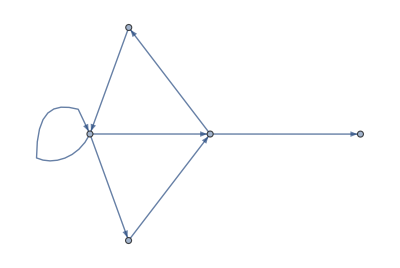
{-Graphics-,{{{1,5}},{{1,5,6}},{{2,14,5}},{{2,14,5,6}}}}

```mathematica
{sg,pl}=FindSubCircuit[g,{1,2},{5,6}]
```

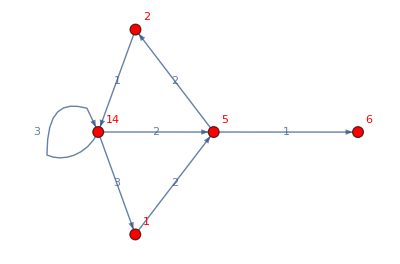

```mathematica
Graph[sg,VertexLabels->Automatic,VertexStyle->Red,VertexSize->0.1,EdgeLabels->"EdgeWeight"]
```

## Step 3: Drosophila Larvae Connectome Test

1. Prepare data

```mathematica
m = Import["all_connections.csv"];
m = m /. x_/;x<=0->Infinity ;
m = 1/m;
m = m /. x_/;x<=0->Infinity ;
```

2. Create and visualize graph

```mathematica
g = WeightedAdjacencyGraph[m];
CommunityGraphPlot[g]
```

-Graphics-

3. Find set of shortest paths and subgraph

```mathematica
{sg,ps}=FindSubCircuit[g,{1,2},{124}]
```

GraphDistance::inv: The argument {124} in GraphDistance[Graph[<288>, <3663>], 1, {124}] is not a valid vertex.

FindPath::inv: The argument {124} in FindPath[Graph[<288>, <3663>], 1, {124}, {GraphDistance[Graph[<288>, <3663>], 1, {124}]}, All] is not a valid vertex.

GraphDistance::inv: The argument {124} in GraphDistance[Graph[<288>, <3663>], 1, {124}] is not a valid vertex.

FindPath::inv: The argument {124} in FindPath[Graph[<288>, <3663>], 1, {124}, {GraphDistance[Graph[<288>, <3663>], 1, {124}]}, All] is not a valid vertex.

{-Graphics-,{FindPath[-Graphics-,1,{124},{GraphDistance[-Graphics-,1,{124}]},All],FindPath[-Graphics-,1,{124},{GraphDistance[-Graphics-,1,{124}]},All]}}

4. Visualize

```mathematica
HighlightGraph[sg,ps,VertexLabels->Automatic,VertexSize->0.3]
```

-Graphics-

## Step 4: C. elegans Connectome

1. Prepare data

```mathematica
m = Import["ce.csv"];
m = m /. x_/;x<=0->Infinity ;
m = 1/m;
m = m /. x_/;x<=0->Infinity ;
```

```mathematica
name = Import["cenames.csv"];
```

```mathematica
justnames=Transpose[name][[2]];
```

```mathematica
nameassoc = Table[i->justnames[[i]],{i,1,Length[justnames]}];
```

```mathematica
a = Association[nameassoc];
```

2. Create and visualize graph

```mathematica
g = WeightedAdjacencyGraph[m];
```

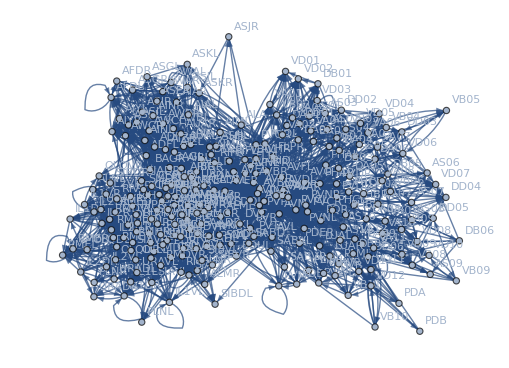

```mathematica
Graph[g,VertexLabels->nameassoc]
```

3. Find set of shortest paths and subgraph

```mathematica
from={"ASEL","ASER"};
(*to = {"SMDDL","SMDDR","SMDVL","SMDVR"};*)
to = {"SMBDL","SMBDR","SMBVL","SMBVR"};
```

```mathematica
{sg,ps}=FindSubCircuit[g,Table[PositionIndex[a][x][[1]],{x,from}],Table[PositionIndex[a][x][[1]],{x,to}]]
```

{-Graphics-,{{{11,92,98,190}},{},{},{},{{12,92,98,190}},{{12,93,99,191}},{{12,92,98,192}},{}}}

```mathematica
HighlightGraph[sg,ps,VertexLabels->nameassoc,VertexSize->0.3]
```

HighlightGraph[-Graphics-,{{{11,92,98,190}},{},{},{},{{12,92,98,190}},{{12,93,99,191}},{{12,92,98,192}},{}},VertexLabels→{1→ASIL,2→ASIR,3→ASJL,4→ASJR,5→AWAL,6→AWAR,7→ASGL,8→ASGR,9→AWBL,10→AWBR,11→ASEL,12→ASER,13→ADFL,14→ADFR,15→AFDL,16→AFDR,17→AWCL,18→AWCR,19→ASKL,20→ASKR,21→ASHL,22→ASHR,23→ADLL,24→ADLR,25→BAGL,26→BAGR,27→URXL,28→URXR,29→ALNL,30→ALNR,31→PLNL,32→PLNR,33→SDQL,34→SDQR,35→AQR,36→PQR,37→ALML,38→ALMR,39→AVM,40→PVM,41→PLML,42→PLMR,43→FLPL,44→FLPR,45→DVA,46→PVDL,47→PVDR,48→ADEL,49→ADER,50→PDEL,51→PDER,52→PHAL,53→PHAR,54→PHBL,55→PHBR,56→PHCL,57→PHCR,58→IL2DL,59→IL2DR,60→IL2L,61→IL2R,62→IL2VL,63→IL2VR,64→CEPDL,65→CEPDR,66→CEPVL,67→CEPVR,68→URYDL,69→URYDR,70→URYVL,71→URYVR,72→OLLL,73→OLLR,74→OLQDL,75→OLQDR,76→OLQVL,77→OLQVR,78→IL1DL,79→IL1DR,80→IL1L,81→IL1R,82→IL1VL,83→IL1VR,84→AINL,85→AINR,86→AIML,87→AIMR,88→RIH,89→URBL,90→URBR,91→RIR,92→AIYL,93→AIYR,94→AIAL,95→AIAR,96→AUAL,97→AUAR,98→AIZL,99→AIZR,100→RIS,101→ALA,102→PVQL,103→PVQR,104→ADAL,105→ADAR,106→RIFL,107→RIFR,108→BDUL,109→BDUR,110→PVR,111→AVFL,112→AVFR,113→AVHL,114→AVHR,115→PVPL,116→PVPR,117→LUAL,118→LUAR,119→PVNL,120→PVNR,121→AVG,122→DVB,123→RIBL,124→RIBR,125→RIGL,126→RIGR,127→RMGL,128→RMGR,129→AIBL,130→AIBR,131→RICL,132→RICR,133→SAADL,134→SAADR,135→SAAVL,136→SAAVR,137→AVKL,138→AVKR,139→DVC,140→AVJL,141→AVJR,142→PVT,143→AVDL,144→AVDR,145→AVL,146→PVWL,147→PVWR,148→RIAL,149→RIAR,150→RIML,151→RIMR,152→AVEL,153→AVER,154→RMFL,155→RMFR,156→RID,157→AVBL,158→AVBR,159→AVAL,160→AVAR,161→PVCL,162→PVCR,163→RIPL,164→RIPR,165→URADL,166→URADR,167→URAVL,168→URAVR,169→RMEL,170→RMER,171→RMED,172→RMEV,173→RMDDL,174→RMDDR,175→RMDL,176→RMDR,177→RMDVL,178→RMDVR,179→RIVL,180→RIVR,181→RMHL,182→RMHR,183→SABD,184→SABVL,185→SABVR,186→SMDDL,187→SMDDR,188→SMDVL,189→SMDVR,190→SMBDL,191→SMBDR,192→SMBVL,193→SMBVR,194→SIBDL,195→SIBDR,196→SIBVL,197→SIBVR,198→SIADL,199→SIADR,200→SIAVL,201→SIAVR,202→DA01,203→DA02,204→DA03,205→DA04,206→DA05,207→DA06,208→DA07,209→DA08,210→DA09,211→PDA,212→DB01,213→DB02,214→DB03,215→DB04,216→DB05,217→DB06,218→DB07,219→AS01,220→AS02,221→AS03,222→AS04,223→AS05,224→AS06,225→AS07,226→AS08,227→AS09,228→AS10,229→AS11,230→PDB,231→DD01,232→DD02,233→DD03,234→DD04,235→DD05,236→DD06,237→VA01,238→VA02,239→VA03,240→VA04,241→VA05,242→VA06,243→VA07,244→VA08,245→VA09,246→VA10,247→VA11,248→VA12,249→VB01,250→VB02,251→VB03,252→VB04,253→VB05,254→VB06,255→VB07,256→VB08,257→VB09,258→VB10,259→VB11,260→VD01,261→VD02,262→VD03,263→VD04,264→VD05,265→VD06,266→VD07,267→VD08,268→VD09,269→VD10,270→VD11,271→VD12,272→VD13},VertexSize→0.3]

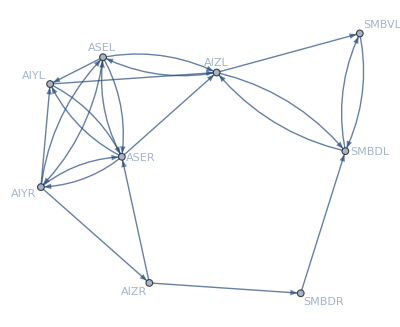

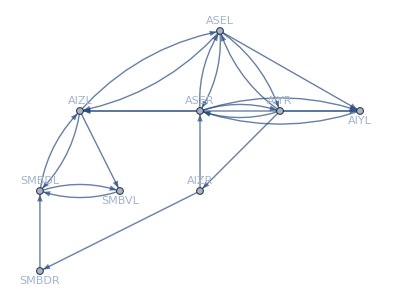

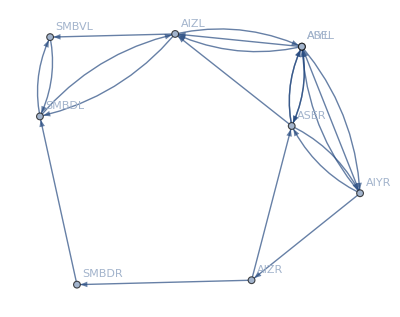

```mathematica
Graph[sg,GraphLayout->"SpringElectricalEmbedding",VertexLabels->nameassoc]
Graph[sg,GraphLayout->"LayeredEmbedding",VertexLabels->nameassoc]
Graph[sg,GraphLayout->"HighDimensionalEmbedding",VertexLabels->nameassoc]
```

{{1,15,2},{1,13,2},{1,12,2}}

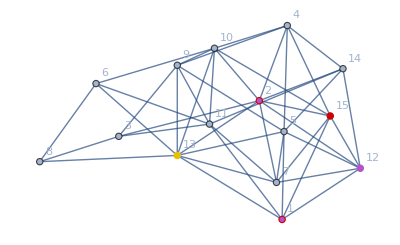

```mathematica
g=RandomGraph[{15,44},VertexLabels->"Name"];
s=1;
t=2;
FindPath[g,s,t,{GraphDistance[g,s,t]},All]
HighlightGraph[g,%]
```